```mathematica
gameOfLife={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
puffer={{1,4},{2,5},{3,1},{3,5},{4,2},{4,3},{4,4},{4,5},{8,1},{9,2},{9,3},{10,3},{11,3},{12,2},{15,1},{15,4},{16,5},{17,1},{17,5},{18,2},{18,3},{18,4},{18,5}};
glider = {{0,1,0},{0,0,1},{1,1,1}};
```

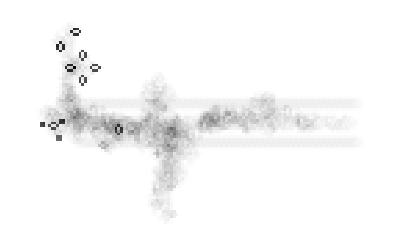

```mathematica
ArrayPlot[Mean[CellularAutomaton[GameOfLife,{SparseArray[Puffer->1],0},200]]]
```

```mathematica
ArrayPlot[#,ImageSize->40,Mesh->True]&/@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{{0,1,0},{0,0,1},{1,1,1}},0},8]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Manipulate[
ArrayPlot[
CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{{0,1,0},{0,0,1},{1,1,1}},0},10][[gen]]
]
,{gen,1,10,1}
]
```

```mathematica
CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{{0,1,0},{0,0,1},{1,1,1}},0},10][[1]]
```

{{0,1,0,0,0},{0,0,1,0,0},{1,1,1,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
life[seed_,ini_,i_]:=Manipulate[
ArrayPlot[
CellularAutomaton[seed,ini,i][[gen]]
]
,{gen,1,i,1}
]
```

```mathematica
b3s23 = {224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}}
```

{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}}

```mathematica
glider = {{{0,1,0},{0,0,1},{1,1,1}},0}
```

{{{0,1,0},{0,0,1},{1,1,1}},0}

```mathematica
life[b3s23,glider,10]
```